# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

ia=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
icolor=reduire[clean@Import[pathResult],reduce];

Show[{ia,ib}]

(*{1,44},{1,102} arbitrary size to make the method faster *)
dim=ImageDimensions[ia];
nx=800/reduce;
ny=700/reduce;

{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,icolor}
ImageDimensions[#]&/@{ia,ib,icolor}
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45}}

## Little functions

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

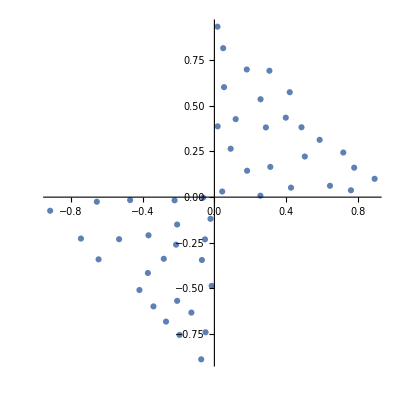

```mathematica
(* Creating list of initial Values *)
r=Random[];
listv0=Select[RandomReal[{-1,1},{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤1)&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0,AspectRatio->Automatic]
```

```mathematica
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,{-2,2},{0,1}]],Point[{p-0.5,y+0.5}]};
```

```mathematica
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
bigTest[steps_,e_,minmaxList_,dis_]:=Block[{depth, resTable,realPVTable,pos,pv,g0},(
Table[
ic=move[ia,dis];
depth=stereoDepth[listv0,ia,ic,minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];


(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[ia,g0],ImageSize->ImageDimensions[ia]*5,ImageResolution->300];

{realPVTable,g0}

,{minmax,minmaxList}]
)]
```

## Big Tests

```mathematica
e=0.0001;
```

#### Full image dis=0.3, step=1

```mathematica
dis=0.5;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
testList={{1,1}}
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

{{1,1}}

#### Display Full image dis=0.3, step=1

```mathematica
dis=0.5;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]];
```

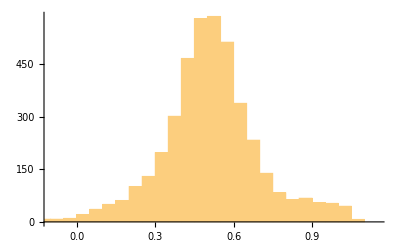

```mathematica
Histogram[Flatten[Subscript[resTable^step, dis][[1,1,All,All,2]]]]
```

```mathematica
wichShow=1;
g1=GraphicsRow[{GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]},ImageSize->500],BarLegend[{RainbowColor[#]&,{0,1}}]}]
```

-Graphics-

#### Little test

```mathematica
Subscript[resTable^step, dis][[1,1,row,All]]
```

{{0.751945,0.569528},{1.87119,0.343429},{2.73895,0.548664},{3.53778,0.892541},{5.28654,-0.941072},{5.75331,0.863822},{6.89398,0.380641},{7.8411,0.364103},{8.78889,0.460889},{9.74756,0.510356},{10.7331,0.517538},{11.8542,0.33972},{12.7906,0.46101},{13.6503,0.731871},{14.8988,0.355522},{15.7245,0.572289},{16.5833,0.689355},{17.6343,0.533309},{19.8145,0.552453},{21.6728,0.977642},{22.8533,0.453167},{23.6998,0.576323},{24.5,0.856073},{25.9604,0.133368},{26.7679,0.528378},{27.8373,0.352874},{28.7377,0.571461},{29.5219,0.74876},{30.9258,0.21291},{31.761,0.536936},{32.6847,0.567589},{34.7911,0.519868},{36.7712,0.534137},{37.6758,0.57085},{38.7596,0.481992},{39.6641,0.678662},{40.9185,0.19878},{41.7882,0.484852},{42.6925,0.591783},{43.6029,0.656192},{44.8803,0.285518},{45.7907,0.467261},{46.7245,0.548678},{47.6202,0.689213},{48.9174,0.205092},{49.7659,0.531231},{50.7762,0.433841},{51.7724,0.48692},{52.665,0.653209},{53.9004,0.237767},{54.7614,0.5407},{55.627,0.642897},{56.7712,0.423333},{57.7243,0.604361},{58.6808,0.4952},{59.8656,0.334094},{60.7726,0.491587},{61.7333,0.521031},{62.7687,0.464739},{63.7743,0.471621},{64.7707,0.47009},{65.8063,0.417946},{66.7742,0.477475},{67.733,0.532236},{68.7135,0.545753},{69.6778,0.615832},{70.5934,0.625945},{71.8258,0.389755},{72.649,0.82882},{74.7368,-1.22324},{74.9047,0.344989},{75.6475,0.805378},{76.8392,0.59799},{78.8817,0.302158},{79.7808,0.480806},{80.703,0.580458},{81.6549,0.59621},{82.5972,0.816902},{83.8295,0.519893},{84.7742,0.431441},{85.8851,0.295015},{86.8082,0.431404},{87.7099,0.596157},{88.5204,0.72753},{89.8891,0.268018},{90.7234,0.620917},{91.864,0.287424},{92.8528,0.356798},{93.7665,0.499206},{94.7128,0.555128},{95.7053,0.54921},{96.7089,0.565641},{98.8526,0.378206},{99.7871,0.455063},{100.771,0.473311},{101.757,0.496163},{102.74,0.512494}}

```mathematica
row=1;
pyrfia=pyrFuncGen[ImageData[ia][[row]],4];
pyrfic=pyrFuncGen[ImageData[move[ia,dis]][[row]],4];
pyrfi=Flatten[{pyrfia,pyrfic},{{2},{1},{3}}];
```

```mathematica
resV=lineTest[listv0,Range[1,103],pyrfi[[1;;4]],e, "ConstrainedNewMethod"];
resV1=Select[resV,(#[[3]]=="converged")&][[All,1;;4]];
Thread[{resV1[[All,4]]-resV1[[All,1]],resV1[[All,1]]+resV1[[All,2]]}]
```

{{0.743353,0.50918},{1.87684,0.333466},{2.73811,0.549548},{3.52432,0.879676},{5.75331,0.863822},{6.89271,0.333915},{7.82752,0.371558},{8.78642,0.460808},{9.74753,0.510406},{10.7336,0.517255},{11.8353,0.352633},{12.7884,0.463077},{13.6381,0.726371},{14.8911,0.336354},{15.7211,0.574528},{16.5739,0.683806},{17.6351,0.537672},{19.8145,0.552453},{21.6728,0.977642},{22.8533,0.453635},{23.6997,0.578193},{24.5324,0.825289},{25.9301,0.149114},{26.7664,0.525561},{27.8343,0.355905},{28.7374,0.571779},{29.5228,0.747944},{30.9031,0.23391},{31.759,0.538622},{32.6854,0.567523},{34.7911,0.519868},{36.7706,0.534667},{37.6757,0.570631},{38.759,0.482641},{39.6647,0.678032},{40.8692,0.244326},{41.788,0.481687},{42.6919,0.59089},{43.5904,0.658828},{44.8558,0.310924},{45.79,0.464901},{46.7236,0.548095},{47.6189,0.690907},{48.8698,0.249483},{49.7666,0.530311},{50.7677,0.442251},{51.7723,0.487017},{52.6523,0.662851},{53.8551,0.28084},{54.7621,0.540032},{55.6305,0.633866},{56.7729,0.421659},{57.7182,0.609498},{58.6798,0.496225},{59.8617,0.336647},{60.7728,0.489536},{61.7331,0.521218},{62.7684,0.465155},{63.7725,0.471224},{64.7712,0.470226},{65.8032,0.420484},{66.7741,0.477549},{67.7316,0.532987},{68.7114,0.545155},{69.6665,0.622276},{70.5866,0.629447},{71.8155,0.399335},{72.6417,0.822616},{74.9038,0.347906},{75.6326,0.83478},{76.837,0.5992},{78.8702,0.314451},{79.7803,0.47958},{80.6991,0.579361},{81.6547,0.597974},{82.5901,0.846345},{83.8282,0.510317},{84.7749,0.416474},{85.8644,0.304261},{86.8071,0.433971},{87.7029,0.600786},{88.5216,0.72716},{89.8718,0.287862},{90.7194,0.624854},{91.8258,0.320553},{92.8503,0.359876},{93.7665,0.498973},{94.7097,0.555383},{95.7031,0.549114},{96.7006,0.569378},{98.8456,0.370767},{99.787,0.452827},{100.77,0.473974},{101.757,0.496106},{102.739,0.513447}}

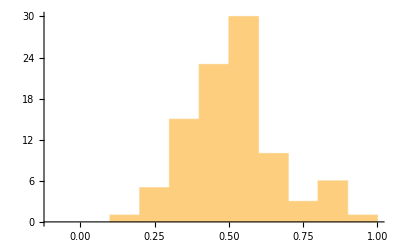

```mathematica
Histogram[resV1[[All,1]]+resV1[[All,2]]]
```

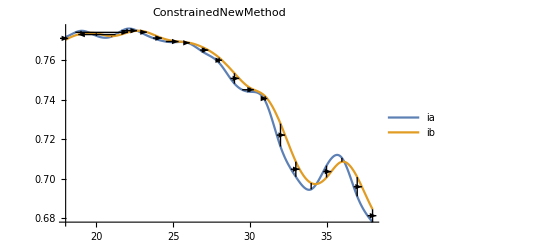

```mathematica
seeAllLine[listv0,Range[18,38],pyrfi[[1;;4]],e, "ConstrainedNewMethod"]
```

#### Full image dis=0.5, step=0.5

```mathematica
dis=0.5;
step=0.5;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=0.5, step=0.5

```mathematica
dis=0.5;
step=0.5;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

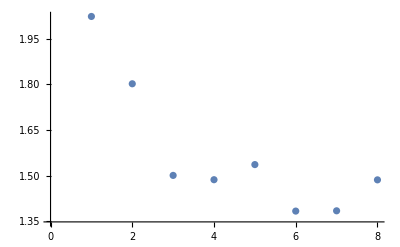

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=3;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=0.1, step=1

```mathematica
dis=0.1;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=0.1, step=1

```mathematica
dis=0.1;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

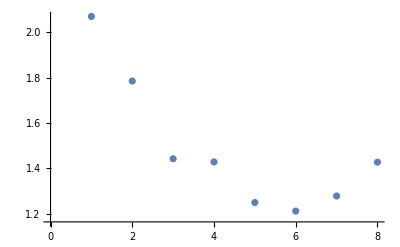

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=1.5, step=1

```mathematica
dis=1.5;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=1.5, step=1

```mathematica
dis=1.5;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

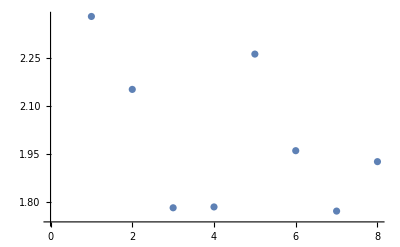

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=1.5, step=0.2

```mathematica
dis=1.5;
step=0.2;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=1.5, step=0.2

```mathematica
dis=1.5;
step=0.2;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

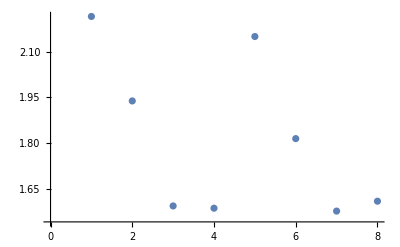

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-